```mathematica
(*Bloque para cargar MaTeX*)
ResourceFunction["MaTeXInstall"][];
ConfigureMaTeX["Ghostscript"->"C:\\Program Files\\gs\\gs10.03.0\\bin\\gswin64c.exe"];
ConfigureMaTeX["pdfLaTeX" -> "C:\\texlive\\2024\\bin\\windows\\pdflatex.exe"]
<<MaTeX`;
MaTeX["x^2"]
```

ConfigureMaTeX[pdfLaTeX→C:\texlive\2024\bin\windows\pdflatex.exe]

ConfigureMaTeX::shdw: Symbol ConfigureMaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

-Graphics-

```mathematica
ν=1/3;
```

Relacion Original simetrica

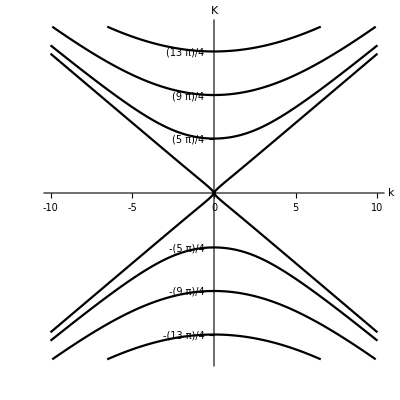

```mathematica
ContourPlot[Sqrt[Kw^2-k^2]*(Kw^2+(1-ν)k^2)^2 *Cosh[Sqrt[Kw^2+k^2]]*Sin[Sqrt[Kw^2-k^2]]-
Sqrt[Kw^2+k^2]*(Kw^2-(1-ν)k^2)^2 *Sinh[Sqrt[Kw^2+k^2]]*Cos[Sqrt[Kw^2-k^2]]==0,{k,-10,10},{Kw,-12,12}, PlotTheme->"Monochrome", Frame->False,Axes->True,AxesLabel->{k,K}, Ticks->{{-10,-5,0,5,10},{-5Pi/4,-9Pi/4, -13Pi/4,5Pi/4,9Pi/4, 13Pi/4}}, MaxRecursion->5]
```

Relacion original antisimetrica

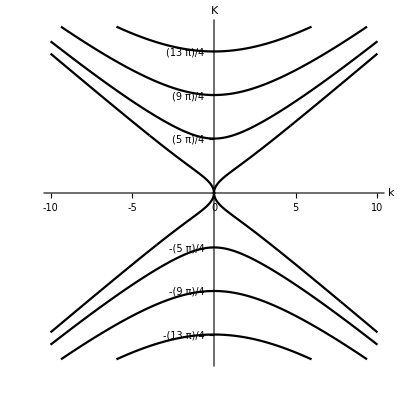

```mathematica
ContourPlot[Sqrt[Kw^2+k^2]*(Kw^2-(1-ν)k^2.)^2 *Sin[Sqrt[Kw^2-k^2]]- 
Sqrt[Kw^2-k^2]*(Kw^2+(1-ν)k^2)^2 *Tanh[Sqrt[Kw^2+k^2]]*Cos[Sqrt[Kw^2-k^2]]==0.,{k,-10,10},{Kw,-12,12}, MaxRecursion->6, PerformanceGoal->"Quality", PlotTheme->"Monochrome", Frame->False,Axes->True,AxesLabel->{k,K}, Ticks->{{-10,-5,0,5,10},{-5Pi/4,-9Pi/4, -13Pi/4,5Pi/4,9Pi/4, 13Pi/4}}]
```

Relacion de dispersion simetrica

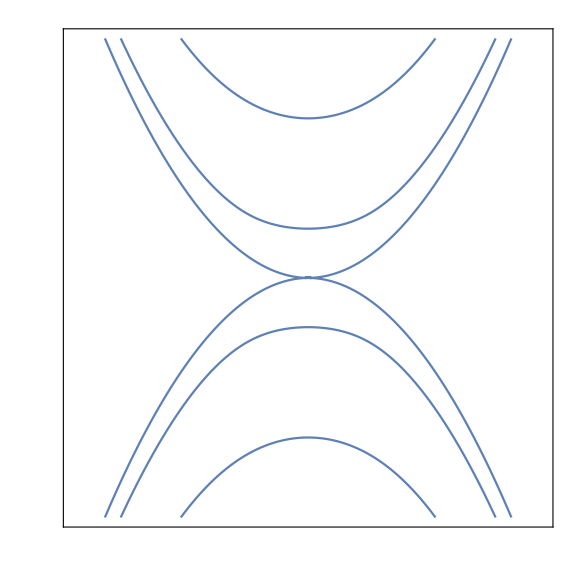

```mathematica
p1 = graficaSimetrica=ContourPlot[Sqrt[Abs[w]-k^2]*(Abs[w]+(1-ν)k^2)^2 *Cosh[Sqrt[Abs[w]+k^2]/2]*Sin[Sqrt[Abs[w]-k^2]/2]-
Sqrt[Abs[w]+k^2]*(Abs[w]-(1-ν)k^2)^2 *Sinh[Sqrt[Abs[w]+k^2]/2]*Cos[Sqrt[Abs[w]-k^2]/2]==0,{k,-20,20},{w,-300,300}, PlotTheme->"Minimal", MaxRecursion->5, ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}]
```

```mathematica
Export["simetrica.pdf", graficaSimetrica]
```

simetrica.pdf

```mathematica
Export["antisimetrica.pdf", antisimetrica]
```

antisimetrica.pdf

Relación de Dispersión Antisimétrica

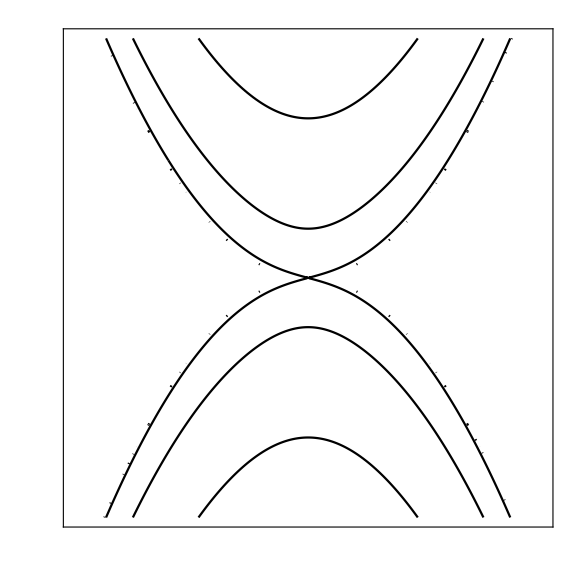

```mathematica
antisimetrica=ContourPlot[Sqrt[Abs[w]+k^2]*(Abs[w]-(1-ν)k^2)^(2) *Cosh[Sqrt[Abs[w]+k^2]/2]*Sin[Sqrt[Abs[w]-k^2]/2]-
Sqrt[Abs[w]-k^2]*(Abs[w]+(1-ν)k^2)^(2) *Sinh[Sqrt[Abs[w]+k^2]/2]*Cos[Sqrt[Abs[w]-k^2]/2]==0,{k,-20,20},{w,-300,300}, PlotTheme->"Monochrome", MaxRecursion->5,  ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}]
```

Despejando a la frecuencia

```mathematica
frecuenciaωSimPositivo[waveNumber_, offset_]:= Re[w/.First[With[{k=waveNumber}, FindRoot[Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]/2]*Sin[Sqrt[w-k^2]/2]-
Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]/2]*Cos[Sqrt[w-k^2]/2]==0,{w,Abs[k]^2+offset}, WorkingPrecision->MachinePrecision]]]];
frecuenciaωSimNegativo[waveNumber_, offset_]:= Re[w/.First[With[{k=waveNumber}, FindRoot[Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]/2]*Sin[Sqrt[w-k^2]/2]-
Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]/2]*Cos[Sqrt[w-k^2]/2]==0,{w,-Abs[k]^2+offset}, WorkingPrecision->MachinePrecision]]]];
frecuenciaωAntiSimPositivo[waveNumber_, offset_]:= Re[w/.First[With[{k=waveNumber}, FindRoot[Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Tan[Sqrt[w-k^2]/2]-
Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Tanh[Sqrt[w+k^2]/2]==0,{w,Abs[k]+offset}, WorkingPrecision->MachinePrecision]]]];
frecuenciaωAntiSimNegativo[waveNumber_, offset_]:= Re[w/.First[With[{k=waveNumber}, FindRoot[Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]/2]*Sin[Sqrt[w-k^2]/2]-
Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]/2]*Cos[Sqrt[w-k^2]/2]==0,{w,-Abs[k]^2+offset}, WorkingPrecision->MachinePrecision]]]];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

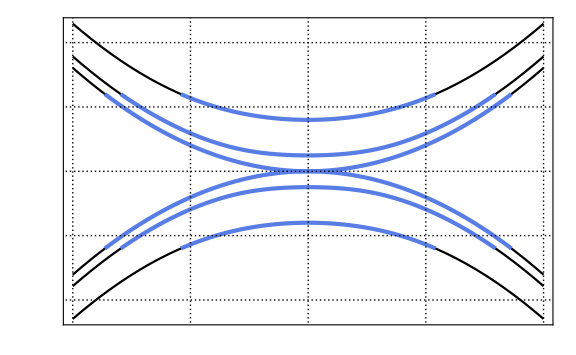

```mathematica
dispersionRelationP1=Plot[frecuenciaωSimPositivo[x,0.0],{x, -20,20},  PlotTheme->"Monochrome", ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-500,500,250]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}];
dispersionRelationP2=Plot[frecuenciaωSimPositivo[x,60.0],{x, -20,20},  PlotTheme->"Monochrome", ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,20]}] (*x axis*),None}
}];
dispersionRelationP3=Plot[frecuenciaωSimPositivo[x,200.0],{x, -20,20},  PlotTheme->"Monochrome", ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}];
dispersionRelationP4=Plot[frecuenciaωSimNegativo[x,0.0],{x, -20,20},  PlotTheme->"Monochrome", ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}];
dispersionRelationP5=Plot[frecuenciaωSimNegativo[x,-60.0],{x, -20,20},  PlotTheme->"Monochrome", ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}];
dispersionRelationP6=Plot[frecuenciaωSimNegativo[x,-200.0],{x, -20,20},  PlotTheme->"Monochrome", ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}];
SimetricDispersionRelation=Show[dispersionRelationP1, dispersionRelationP2, dispersionRelationP3, dispersionRelationP4, dispersionRelationP5, dispersionRelationP6, p1, PlotRange->All]
```

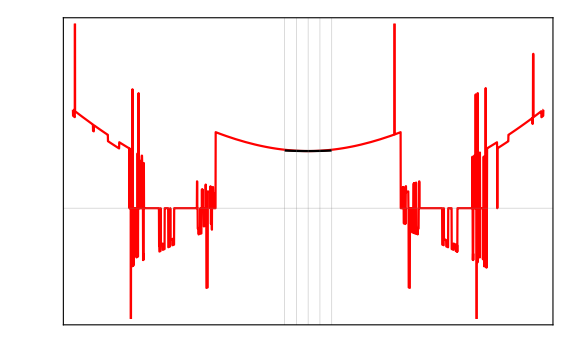

```mathematica
dispersionRelationAntiSP1=Plot[frecuenciaωAntiSimPositivo[x,60.0],{x, -10,10},PlotStyle->Red,ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-500,500,250]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-1,1,0.5]}] (*x axis*),None}
}];
dispersionRelationAntiSP2=Plot[frecuenciaωSimPositivo[x,60.0],{x, -1,1},  PlotTheme->"Monochrome", ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,20]}] (*x axis*),None}
}];(*
dispersionRelationP3=Plot[frecuenciaωSimPositivo[x,200.0],{x, -20,20},  PlotTheme->"Monochrome", ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}];
dispersionRelationP4=Plot[frecuenciaωSimNegativo[x,0.0],{x, -20,20},  PlotTheme->"Monochrome", ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}];
dispersionRelationP5=Plot[frecuenciaωSimNegativo[x,-60.0],{x, -20,20},  PlotTheme->"Monochrome", ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}];
dispersionRelationP6=Plot[frecuenciaωSimNegativo[x,-200.0],{x, -20,20},  PlotTheme->"Monochrome", ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}];*)
Show[dispersionRelationAntiSP1, dispersionRelationAntiSP2, PlotRange->All]
```